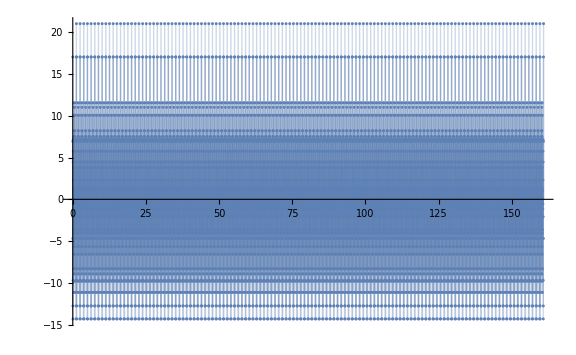

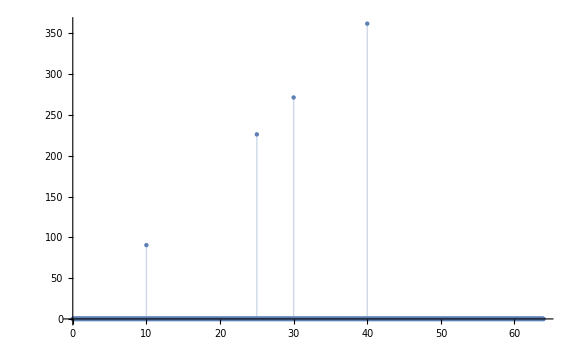

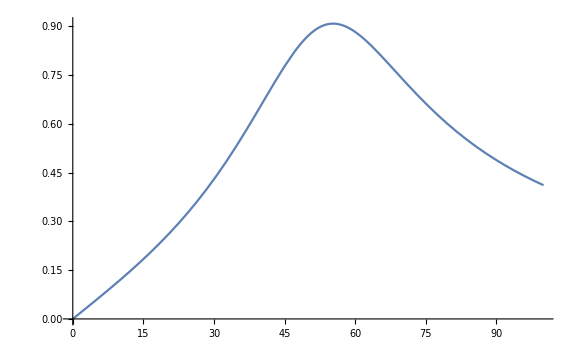

0.3364499519834

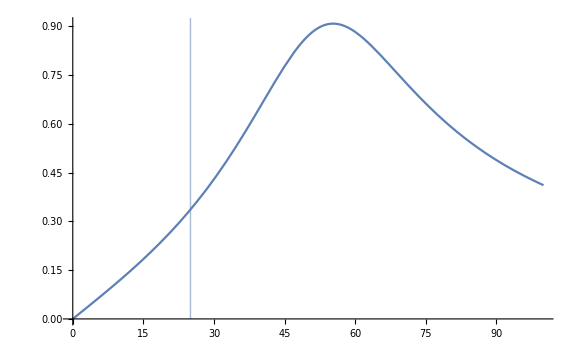

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
L1=SetPrecision[12.8164199928364,15];
L2=SetPrecision[0.816960555966298,15];
C1=SetPrecision[0.0000108152696951576,17];
C2=SetPrecision[0.000014386629751342,17];
R1=SetPrecision[118.576345807595,15];
R2=SetPrecision[38.4834524145474,15];
R3=SetPrecision[1077.4489489342,15];
R4=SetPrecision[506.185979863507,15];
dt=SetPrecision[0.0196349540849362,15];
N1=8192;

inputSignal=ReadList["E:\\downloads\\15.txt"];
ListPlot[Table[{(i-1)*dt,inputSignal[[i]]},{i,1,N1}],Filling->Axis]
fs=Fourier[inputSignal];
spectr=Table[{2 π/(dt*N1) (i-1),Abs@fs[[i]]},{i,1,Length@fs/5}];
ListPlot[spectr,Filling->Axis]
h=Select[spectr,#[[2]]>1&][[2]];
Z1[w_]=R4+Divide[1,I*w*C2];
Z2[w_]=1/(I*w*C1)+R2+I*w*L2+R3;
Zpar[w_]=1/(1/Z1[w]+1/Z2[w]);
I1[w_]=Uin/(R1+I*w*L1+Zpar[w]);
Upar[w_]=I1[w]*Zpar[w];
Ipar2[w_]=Upar[w]/Z2[w];
Uout[w_]=Ipar2[w]*R3;
H[w_]=Uout[w]/Uin;
Plot[Abs[H[w]],{w,0,100}]
Abs@H[h[[1]]]
Show[Plot[Abs@H[w],{w,0,100}],ListPlot[{h},Filling->Axis]]
```